## DisentangleVertices-Example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 05:12:51
using xCellerator 0.90 and XSSA 1204002

Create a tissue with a point and an edge that aren't used.

```mathematica
v={{0,0}, {1, 0}, {1, 2}, {1, .5}};
e={{1,2},  {2, 3}, {3, 1}}; 
c={{1,2,3}}; 
q=Tissue[v,e,c]
```

Tissue[{{0,0},{1,0},{1,2},{1,0.5}},{{1,2},{2,3},{3,1}},{{1,2,3}}]

Show the entangled vertices, if any, on each edge.

```mathematica
EntangledVertices[q]
```

{{},{4},{}}

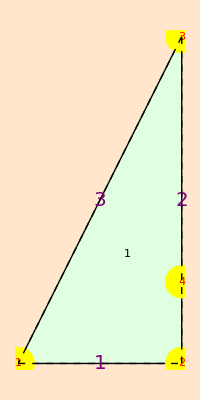

```mathematica
ShowTissue[q, "Vertices"-> {Yellow, PointSize[.06]}, "VertexNumbers"->{Red, FontSize-> 20}, "CellNumbers"-> True , "EdgeNumbers"-> True, "EdgeNumberStyle"-> {Black, FontSize-> 20, FontColor-> Purple, Background-> White}, "All"-> True , "BoundaryStyle"-> Dashed, Background-> LightOrange]
```

Disentangling replaces edges 2 from vertex 2 to vertex 3 with two edges, one from 2 to 4 and one from 4 to 3.

```mathematica
q1=DisentangleVertices[q]
```

Tissue[{{0,0},{1,0},{1,2},{1,0.5}},{{1,2},{3,4},{1,3},{2,4}},{{1,4,2,3}}]

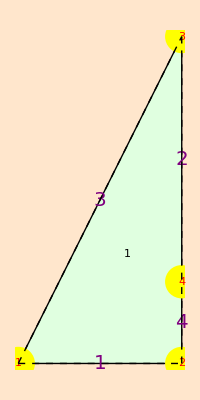

```mathematica
ShowTissue[q1, "Vertices"-> {Yellow, PointSize[.06]}, "VertexNumbers"->{Red, FontSize-> 20}, "CellNumbers"-> True , "EdgeNumbers"-> True, "EdgeNumberStyle"-> {Black, FontSize-> 20, FontColor-> Purple, Background-> White}, "All"-> True , "BoundaryStyle"-> Dashed, Background-> LightOrange]
```